```mathematica
Unset[density1];
Unset[density2];
Unset[p1];
Unset[p2];
density1=ConstantArray[0,{side,side}];
density2=ConstantArray[0,{side,side}];
p1=Table[{k,ConstantArray[0,{side,side}]},{k,300}];
p2=Table[{k,ConstantArray[0,{side,side}]},{k,300}];
matches=100;
Do[
Unset[gamefile];
filename=ToString[StringForm["/home/ariel/Desktop/Jogo_ciencia/jogo_da_ciencia_data/game_``.dat",match]];gamefile=Import[filename, "Numeric"->False];turns=Dimensions[gamefile]⟦1⟧;
size=StringLength@gamefile⟦1⟧⟦1⟧;
side=Sqrt[StringLength@gamefile⟦1⟧⟦1⟧]; 
Do[
Do[
Do[
If[ToExpression@StringTake[gamefile⟦k⟧⟦1⟧,{(i-1)side+j }]==1,density1⟦i⟧⟦j⟧+=1];
If[ToExpression@StringTake[gamefile⟦k⟧⟦1⟧,{(i-1)side+j }]==2,density2⟦i⟧⟦j⟧+=1];
If[ToExpression@StringTake[gamefile⟦k⟧⟦1⟧,{(i-1)side+j }]==1,p1⟦k⟧⟦2⟧⟦i⟧⟦j⟧+=1];
If[ToExpression@StringTake[gamefile⟦k⟧⟦1⟧,{(i-1)side+j }]==2,p2⟦k⟧⟦2⟧⟦i⟧⟦j⟧+=1];
,{i,side}]
,{j,side}]
,{k,turns}]
,{match,matches}]
```

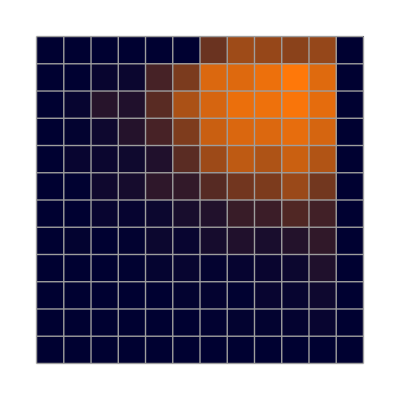
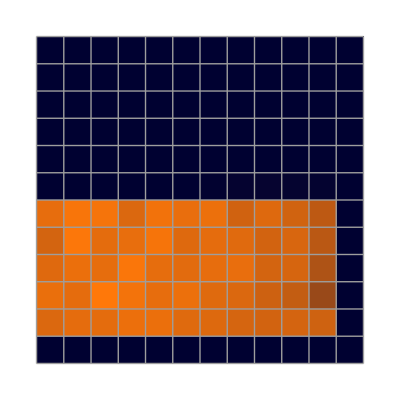

```mathematica
{ArrayPlot[density1,Mesh->True,ColorFunction->"RustTones"],ArrayPlot[density2,Mesh->True,ColorFunction->"RustTones"]}
```

```mathematica
Manipulate[ListPlot3D[p1⟦k⟧⟦2⟧,Mesh->None,InterpolationOrder->0,ImageSize->Large, Filling->Bottom,Mesh->None,ColorFunction->"SunsetColors",PlotRange->{{1,12},{1,12},{-0.1,50}}],{k,1,120,1}]
```

```mathematica
Anim=Table[ListPlot3D[p1⟦k⟧⟦2⟧,Mesh->None,InterpolationOrder->0,ImageSize->Large, Filling->Bottom,Mesh->None,ColorFunction->"SunsetColors",PlotRange->{{1,12},{1,12},{-0.1,50}}],{k,1,120,1}];
```

```mathematica
Export["zombie.gif",Anim,"GIF","AnimationRepetitions"->∞]
```

zombie.gif

```mathematica
Show[
ListPlot3D[density2,Mesh->None,InterpolationOrder->6
,Mesh->None,ColorFunction->"RustTones", PlotStyle->Directive[Opacity[0.9],Red],PlotRange->{{1,12},{1,12},{-100.5,2500}}],
ListPlot3D[density1,Mesh->None,InterpolationOrder->0,Mesh->None,ColorFunction->"Aquamarine", PlotStyle->Directive[Opacity[0.9],Blue],PlotRange->{{1,12},{1,12},{-100.5,2500}}]
]
```

-Graphics3D-